```mathematica
Ep = 1108;
```

```mathematica
measCond = 1.55*^-9;
```

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
qMaxF[Ep_,Tm_]:=1+2(√(Ep/Tm))/Erfc[-√(Ep/Tm)] NIntegrate[Erfc[x],{x,-√(Ep/Tm),∞}]
```

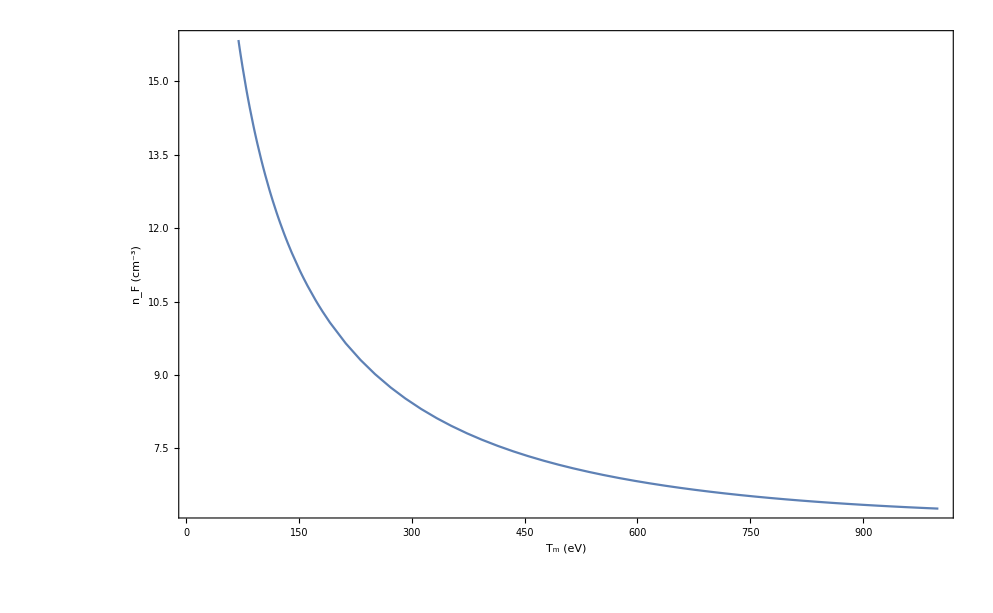

```mathematica
Plot[measCond/preFactor * √Tm *qMaxF[Ep,Tm],{Tm,10,1000},FrameLabel->{StringForm["T_m (eV)"],StringForm["n_F (cm^-3)"]},LabelStyle->(FontSize->18),Frame->True,ImageSize->600]
```

### Now kappa cases

```mathematica
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *qMaxF[Ep,Tm]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

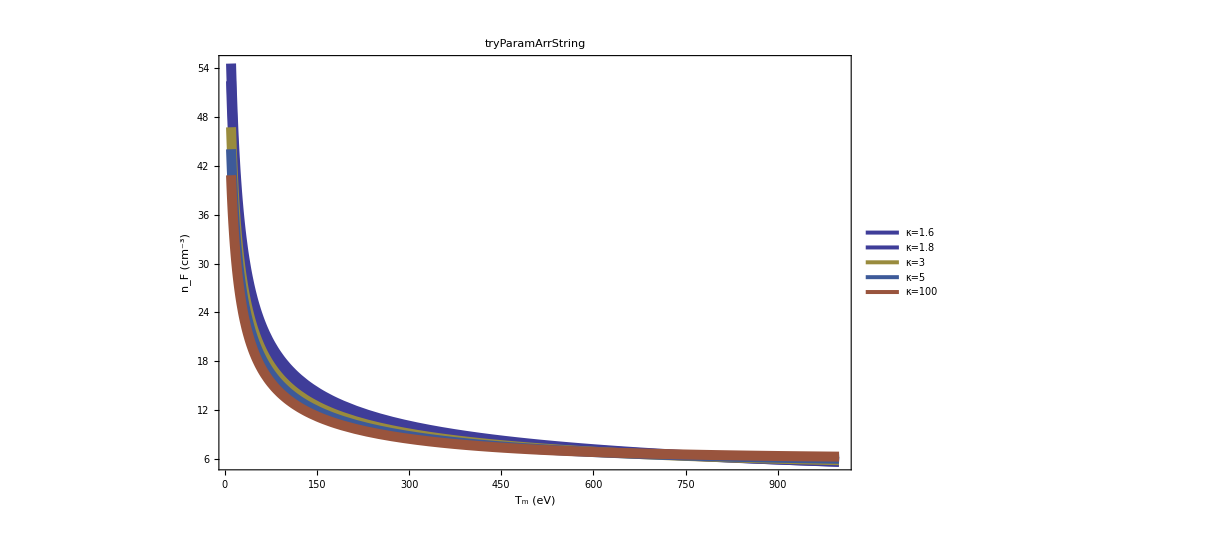

```mathematica
Show[Table[Plot[Legended[funker[Ep,Tm(1-3/(2 k)),k,measCond],StringForm["κ=`1`",NumberForm[k,2]]],{Tm,10,1000},PlotStyle->Directive[ColorData[1][k],Thickness[0.008]],PlotRange->{All,All},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,LabelStyle->(FontSize->18),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_F (cm^-3)"]},ImageSize->900],{k,{1.6,1.8,3,5,100}}]]
```

```mathematica
kappas=Reverse[{1.525,1.6,1.75,2.0,2.45,3,7,1000}];
```

```mathematica
tick = 0.002;
```

```mathematica
styles=Flatten@Table[{Directive[color,Thickness[tick]],Directive[Dashed,color,Thickness[tick]],Directive[DotDashed,color,Thickness[tick]],Directive[Dotted,color,Thickness[tick]]},{color,{Black,Gray}}];
```

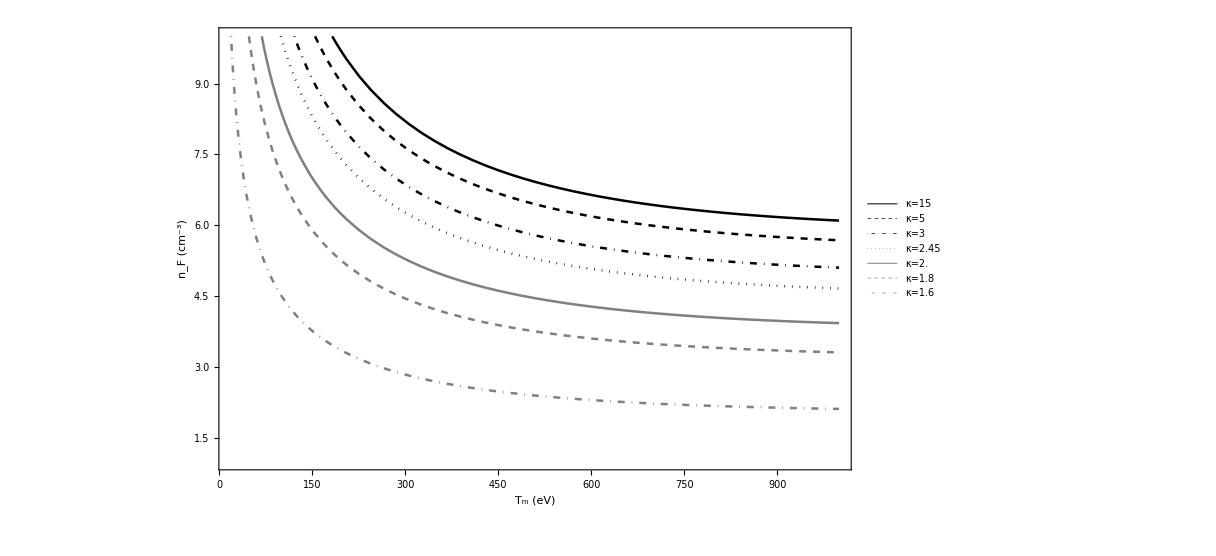

```mathematica
Show[Table[Plot[Legended[funker[Ep,Tm,kappas[[k]],measCond],StringForm["κ=`1`",NumberForm[kappas[[k]],3]]],{Tm,1,1000},PlotStyle->styles[[k]],PlotRange->{All,{1,10}},PlotLegends->LineLegend[Automatic],LabelStyle->(FontSize->18),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_F (cm^-3)"]},ImageSize->900],{k,{1,2,3,4,5,6,7}}]]
```

### Now with labels instead of a legend

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotRange->{All,{1,10}},PlotLegends->LineLegend[Automatic],LabelStyle->(FontSize->18),Frame->True,PlotLabels ->StringForm["κ=`1`",NumberForm[kappas[[k]],3]] ,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_F (cm^-3)"]},ImageSize->900],{k,{1,2,3,4,5,6,7}}]]
```

-Graphics-

### Now placed nicely

```mathematica
placeList={Scaled[1.1],Below,Below,Below,Below,Below,Below,Scaled[1.1]};
```

```mathematica
nDigs={3,3,3,3,3,3,3,4};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[4]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}];
```

```mathematica
kappaLabels[[1]]=StringForm["Maxwellian"];
```

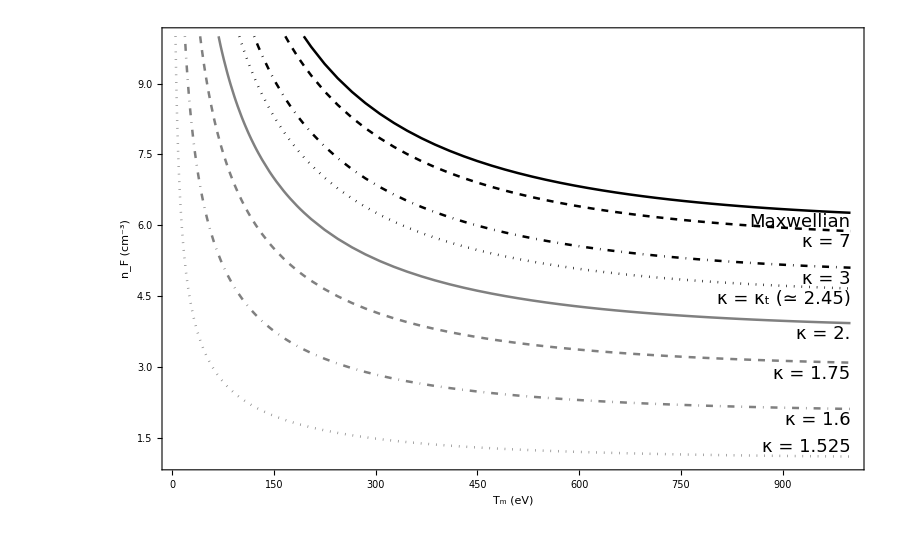

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotRange->{All,{1,10}},PlotLegends->LineLegend[Automatic],LabelStyle->(FontSize->18),Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],FrameLabel->{StringForm["T_m (eV)"],StringForm["n_F (cm^-3)"]},ImageSize->900],{k,{1,2,3,4,5,6,7,8}}]]
```